Number Theory

Introduction to Mathematica

## Inputting Basic Mathematica Expressions

```mathematica
2*3^5+12-2
```

496

```mathematica
(Sin[Pi/2]+12!*Sqrt[12])/ⅇ^4
```

(1+958003200 √3)/ⅇ^4

Mathematica is a Computer Algebra System (CAS), and performs its calculations as exactly as possible. To get approximate decimal value use following:

```mathematica
N[(Sin[Pi/2]+12!*Sqrt[12])/ⅇ^4]
```

3.03913×10^7

```mathematica
(Sin[Pi/2]+12!*Sqrt[12.])/ⅇ^4
```

3.03913×10^7

Basic algebra examples:

```mathematica
3xˆ2+2xˆ3+3
```

3+3 xˆ2+2 xˆ3

```mathematica
3x^4*3y^2
```

9 x^4 y^2

```mathematica
alice+bob
%+2
%+5
```

alice+bob

2+alice+bob

7+alice+bob

```mathematica
alice+bob;
%+2;
%+5
```

7+alice+bob

## Variables

```mathematica
A=2
A 
A+2 
A^10
```

2

2

4

1024

```mathematica
fx=3x^3+2x^2+3x
```

3 x+2 x^2+3 x^3

```mathematica
fx+2x
```

5 x+2 x^2+3 x^3

Substitution operator (/.)

```mathematica
fx /.x->3
fx/.x-> a^(1/2)
fx
```

108

3 √a+2 a+3 a^(3/2)

3 x+2 x^2+3 x^3

Plotting variables

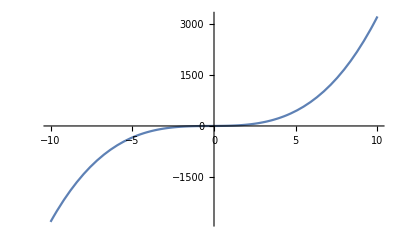

```mathematica
Plot[fx,{x,-10,10}]
```

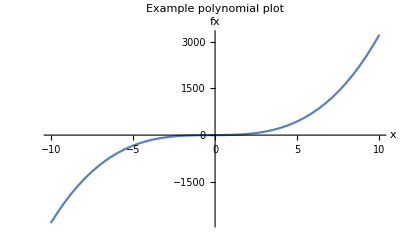

```mathematica
Show[%39,AxesLabel->{HoldForm[x],HoldForm[fx]},PlotLabel->HoldForm[Example polynomial plot],LabelStyle->{FontFamily->"Roboto",10,GrayLevel[0]}]
```

With the = operator, the expression to be assigned is evaluated first, and then assigned to the variable. With the := operator, the expression being assigned is not evaluated at all before assignment to a variable, but is instead evaluated each time the variable is used. This is called a delayed definition.

```mathematica
x:=2^4
```

```mathematica
x=2^4
```

16

## Functions

Functions are written in the form of Name[argument, argument, ...] where name is the name of the function, and argument, argument, . . . is a comma separated list of the function arguments. 
Examples:

```mathematica
FactorInteger[1573]
```

{{11,2},{13,1}}

```mathematica
Clear[x]
```

```mathematica
Factor[x^4-2x^3-13x^2+14x+24]
```

(-4+x) (-2+x) (1+x) (3+x)

```mathematica
Simplify[(x^2+x)/(x^3+2x)]
```

(1+x)/(2+x^2)

```mathematica
Collect[x^2*y+x*y+x^2*z+x*z+x*y^2*z^2,x]
```

x^2 (y+z)+x (y+z+y^2 z^2)

## Lists, Sets, and Sequences

```mathematica
{1,2,3} 
{fx,5,bob}
```

{1,2,3}

{3 x+2 x^2+3 x^3,5,bob}

Nested list:

```mathematica
L1={a,b,c};
L2={1,2,3};
L3={i,ii,iii};
{L1,L2,L3}
```

{{a,b,c},{1,2,3},{i,ii,iii}}

```mathematica
Join[L1,L2,L3]
```

{a,b,c,1,2,3,i,ii,iii}

```mathematica
{i,j,k}={1,2,3}
```

{1,2,3}

```mathematica
i
j
k
```

1

2

3

Indexing operator ([[...]]), or alternatively through the Part function.

```mathematica
S={a,b,c,d,e,f,g,h,i,j}
```

{a,b,c,d,e,f,g,h,1,2}

```mathematica
Part[S,3]
S[[1]]
S[[0]]
```

c

a

List

```mathematica
j[[0]]
```

Integer

```mathematica
S[[{2,4,6,8}]]
```

{b,d,f,h}

```mathematica
S[[5;;8]]
```

{e,f,g,h}

Each of set functions will always produce a list whose elements are sorted, and with no duplicates.

```mathematica
Union[{3,1,2,2,1}]
```

{1,2,3}

```mathematica
Intersection[{1,2,3,5},{4,2,3}]
```

{2,3}

```mathematica
Complement[{1,2,3,5},{4,2,3}]
```

{1,5}

Fairly predictable pattern use Table Function. Table[x_n, {n, a, b}]

```mathematica
Table[x,{4}]
```

{x,x,x,x}

```mathematica
Table[k^2,{k,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

## Sums and Products

```mathematica
Sum[k^2,{k,1,10}]
```

385

```mathematica
Total[Table[k^2,{k,1,10}]]
```

385

```mathematica
Sum[1/k^2,{k,1,Infinity}]
```

π^2/6

```mathematica
Product[k^2,{k,1,10}]
```

13168189440000

## Pre-, Post-, and Infix Function Notation

```mathematica
N[Sqrt[Sin[3/2]]]
```

0.998747

```mathematica
Sqrt[Sin[3/2]]//N
```

0.998747

```mathematica
N@Sqrt[Sin[3/2]]
```

0.998747

```mathematica
{1,2,3}~Join~{3,4,5}
```

{1,2,3,3,4,5}